## Homework 1

### Problem 2.3

#### Graph

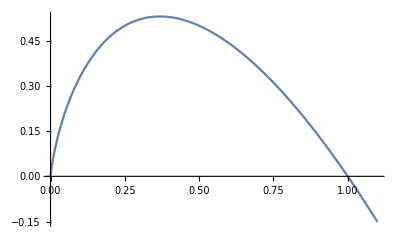

```mathematica
Plot[{-x Log[2,x]},{x,0,1.1}]
```

#### Functional Description

Define Simplification

```mathematica
FSc2p3[aa_]:=FullSimplify[aa,Assumptions->{pi∈Reals,pi≥0,p1∈Reals,p2∈Reals,p3∈Reals,p1≥0,p2≥0,p3≥0}]
```

Define Function

```mathematica
H[x_]:=-x Log[2,x]
H[pi]//FSc2p3
```

-(pi Log[pi])/Log[2]

Plot it

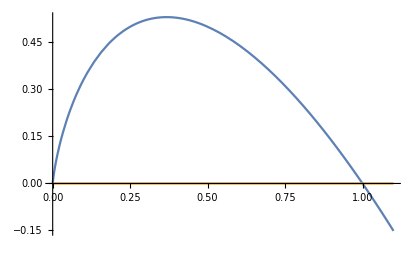

```mathematica
Plot[{H[x],H[x]+x Log[2,x]},{x,0,1.1}]
```

First and Second derivatives

```mathematica
D[H[x],x]//FSc2p3
D[ D[H[x],x], x]//FSc2p3
```

-(1+Log[x])/Log[2]

-1/(x Log[2])

Find first derivative root, plot of 1st derivative, and plot of 1st & 2nd derivatives

{{x→0.367879}}

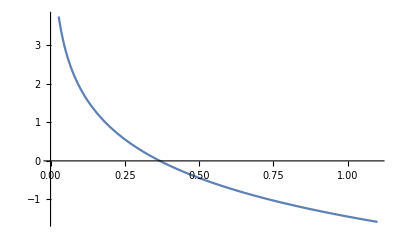

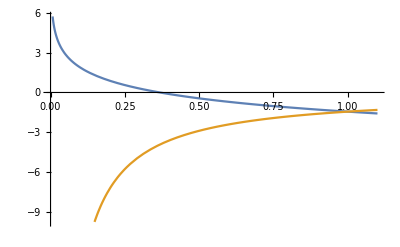

```mathematica
NSolve[0==FSc2p3[D[H[x0],x0]/.{x0->x}],x]
Plot[{FSc2p3[D[H[x0],x0]/.{x0->x}]},{x,0,1.1}]
Plot[{FSc2p3[D[H[x0],x0]/.{x0->x}],FSc2p3[D[H[x0],{x0,2}]/.{x0->x}]},{x,0,1.1}]
```

Solve for root symbolically and numerically

```mathematica
Solve[{0==D[H[x],x]},x]//FSc2p3
```

{{x→1/ⅇ}}

```mathematica
Solve[{0==D[H[x],x]},x]//N
FindMaximum[FSc2p3[H[x]/.{x->pi}],pi]//FSc2p3
```

{{x→0.367879}}

{0.530738,{pi→0.367879}}